This is one suggestion as to how to build up a module. Say we want to find the intersection point of two BesselFunctions. The definition of the BesselFunction is defined explicitly in f[n, x]. Then, a plot is generated and the first intersection of two BesselFunctions are found. This is done with explicit values of n.

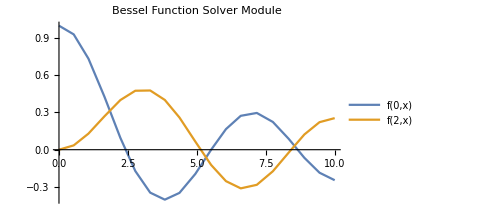

1.84118

0.316028

```mathematica
Clear[f, plot, root]
f[n_,x_]:=Sum[((-1)^k(x/2)^(n+2k))/(k!Gamma[n+k+1]),{k,0,Infinity}]
(*Plot of two functions*)
plot=Plot[{f[0,x],f[2,x]},{x,0,10},PlotPoints->10,MaxRecursion->1,PlotLabel->"Bessel Function Solver Module",PlotLegends->"Expressions",ImageSize->Medium]
(*x value of first intersection*)
root=x/.FindRoot[f[0,x]==f[2,x],{x,2}]
(*y-value of first intersection*)
f[0,root]
```

Using the above procedure as a guiding structure, we can generalize this for arbitrary values of n. 
Here’s an example of a Module in action. The following module take three inputs: n1, n2, and xguess. 

	- n1 is the order of the first BesselFunction
	- n2 is the order of the second BesselFunction
	- xguess is the starting value for the numeric search of the intersection of the two BesselFunctions.

```mathematica
plotSolveMod[n1_,n2_,xguess_]:=Module[{plot,root},
f[n_,x_]:=Sum[((-1)^k(x/2)^(n+2k))/(k!Gamma[n+k+1]),{k,0,Infinity}];
plot=Plot[{f[n1,x],f[n2,x]},{x,0,10},PlotPoints->10,MaxRecursion->1,PlotLabel->"Bessel Function Solver Module",PlotLegends->"Expressions",ImageSize->Medium];
root=x/.FindRoot[f[n1,x]==f[n2,x],{x,xguess}];
{plot,root,f[n1,root]}
]
```

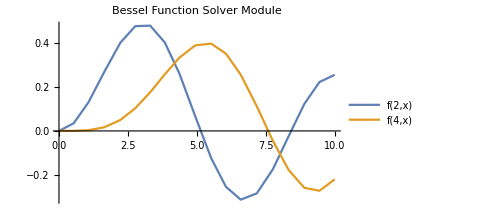
{-Graphics-,4.20119,0.310194}

```mathematica
plotSolveMod[2,4,4]
```